Analysis from diploids from a chromosomal perspective. Following approach is to find out how the chromosomes change over time when selection occurs at a diploid level. 
Step1. Try finding a recursion equation for chromosomal stage based on growth rates for diploids.

## Diploids

```mathematica
1/2*(na[t]+nA[t])*(na[t]/(na[t]+nA[t]))^2
```

na[t]^2/(2 (na[t]+nA[t]))

```mathematica
1/2*(na[t]+nA[t])*(nA[t]/(na[t]+nA[t]))^2
```

nA[t]^2/(2 (na[t]+nA[t]))

Determine based on HWE what the diploid population looks like.

```mathematica
naa[t]:=1/2*(na[t]+nA[t])*(na[t]/(na[t]+nA[t]))^2
nAa[t]:=1/2*(na[t]+nA[t])*(na[t]/(na[t]+nA[t]))*(nA[t]/(na[t]+nA[t]))*2
nAA[t]:=1/2*(na[t]+nA[t])*(nA[t]/(na[t]+nA[t]))^2
```

These diploids increase exponentially with growthrates

```mathematica
naa[t+1]:=naa[t]*Raa;
nAa[t+1]:=nAa[t]*RAa;
nAA[t+1]:=nAA[t]*RAA;
```

```mathematica
naa[t]*Raa
```

(Raa na[t]^2)/(2 (na[t]+nA[t]))

The diploids at t+1 can be translated back to chromosomes by:

```mathematica
na[t+1]:=2*naa[t+1]+nAa[t+1]//Simplify
nA[t+1]:=2*nAA[t+1]+nAa[t+1]//Simplify
```

So the chromosomes form one generation to the next is :

```mathematica
na[t+1]
nA[t+1]
```

(na[t] (Raa na[t]+RAa nA[t]))/(na[t]+nA[t])

(nA[t] (RAa na[t]+RAA nA[t]))/(na[t]+nA[t])

```mathematica
param={Raa->1.1,RAa->1.1,RAA->0.9};
```

Step 2 : Itterate RHS.

```mathematica
Clear[simulatefrac]
simulatefrac[t_,Raa_,RAa_,RAA_]:=simulatefrac[t,Raa,RAa,RAA]=
Block[{
fracA=simulatefrac[t-1,Raa,RAa,RAA][[1]],
fraca=simulatefrac[t-1,Raa,RAa,RAA][[2]],
nA=simulatefrac[t-1,Raa,RAa,RAA][[3]],
na= simulatefrac[t-1,Raa,RAa,RAA][[4]]},

newfracA=(1/2*fracA+1/2*fraca)*(na/(na+nA))+(fracA)*(nA/(na+nA));
newfraca=(1/2*fracA+1/2*fraca)*(nA/(na+nA))+(fraca)*(na/(na+nA));
newnA=nA/(na+nA)(RAa na+RAA nA);
newna=na/(na+nA) (Raa na+RAa nA);
{newfracA,newfraca,newnA,newna} 
]
simulatefrac[0,Raa/.param,RAa/.param,RAA/.param]={1,0,100,2};
```

```mathematica
simulatefrac[1,Raa/.param,RAa/.param,RAA/.param]
```

{101/102,25/51,90.3922,2.2}

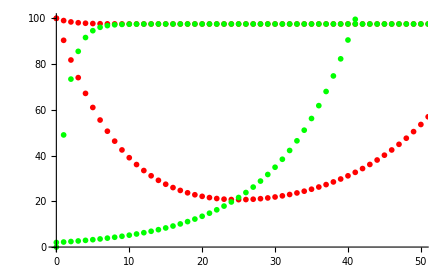

```mathematica
Show[
ListPlot[Table[{t,100*simulatefrac[t,Raa/.param,RAa/.param,RAA/.param][[1]]},{t,0,100}],PlotStyle->{Dotted,Red},PlotRange->{{0,50},{0,100}}],
ListPlot[Table[{t,100*simulatefrac[t,Raa/.param,RAa/.param,RAA/.param][[2]]},{t,0,100}],PlotStyle->{Dotted,Green},PlotRange->{{0,50},{0,100}}],
ListPlot[Table[{t,simulatefrac[t,Raa/.param,RAa/.param,RAA/.param][[3]]},{t,0,100}],PlotStyle->{Red},PlotRange->{{0,50},{0,50}}],
ListPlot[Table[{t,simulatefrac[t,Raa/.param,RAa/.param,RAA/.param][[4]]},{t,0,100}],PlotStyle->{Green},PlotRange->{{0,50},{0,50}}]
]
```

To what extend is the initial fase dominated by the growthrates of the Heterozygotes and the homozygote resident?

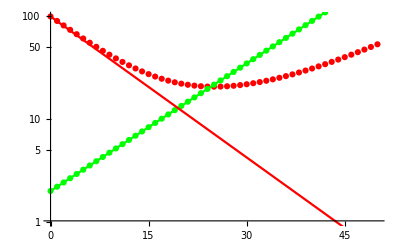

```mathematica
Show[
ListLogPlot[Table[{t,simulatefrac[t,Raa/.param,RAa/.param,RAA/.param][[3]]},{t,0,50}],PlotStyle->{Red},PlotRange->{{0,50},{1,100}}],
ListLogPlot[Table[{t,simulatefrac[t,Raa/.param,RAa/.param,RAA/.param][[4]]},{t,0,50}],PlotStyle->{Green},PlotRange->{{0,50},{0,100}}],
LogPlot[2*(RAa/.param)^t,{t,0,50},PlotStyle->Green],
LogPlot[100*(RAA/.param)^t,{t,0,50},PlotStyle->Red]
]
```

My guess is that as the residents growthrate becomes smaller, this will lead to more homozgotes of the invader, therefore making the invader growth more dependend on the homozygotes growthrate. 
Same goes for increasing the heterozygous growthrate. This will make the change faster towards homozygote stage. We prefer the invader population to stay in heterozygotes and the resident to stay in homozygotes..  

So for this approximation to make sense, RAA can not be to small and RAa can not be to big.. Otherwise this happens:

```mathematica
param={Raa->1,RAa->1.5,RAA->0.2};
Clear[simulatefrac]
simulatefrac[t_,Raa_,RAa_,RAA_]:=simulatefrac[t,Raa,RAa,RAA]=
Block[{
fracA=simulatefrac[t-1,Raa,RAa,RAA][[1]],
fraca=simulatefrac[t-1,Raa,RAa,RAA][[2]],
nA=simulatefrac[t-1,Raa,RAa,RAA][[3]],
na= simulatefrac[t-1,Raa,RAa,RAA][[4]]},

newfracA=(1/2*fracA+1/2*fraca)*(na/(na+nA))+(fracA)*(nA/(na+nA));
newfraca=(1/2*fracA+1/2*fraca)*(nA/(na+nA))+(fraca)*(na/(na+nA));
newnA=nA/(na+nA)(RAa na+RAA nA);
newna=na/(na+nA) (Raa na+RAa nA);
{newfracA,newfraca,newnA,newna} 
]
simulatefrac[0,Raa/.param,RAa/.param,RAA/.param]={1,0,100,2};
```

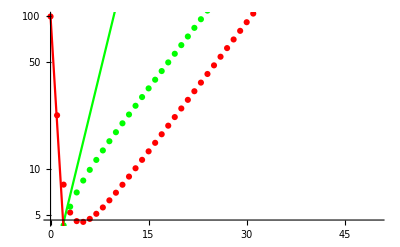

```mathematica
Show[
ListLogPlot[Table[{t,simulatefrac[t,Raa/.param,RAa/.param,RAA/.param][[3]]},{t,0,50}],PlotStyle->{Red},PlotRange->{{0,50},{0,100}}],
ListLogPlot[Table[{t,simulatefrac[t,Raa/.param,RAa/.param,RAA/.param][[4]]},{t,0,50}],PlotStyle->{Green},PlotRange->{{0,50},{0,100}}],
LogPlot[2*(RAa/.param)^t,{t,0,50},PlotStyle->Green],
LogPlot[100*(RAA/.param)^t,{t,0,50},PlotStyle->Red]
]
```

If we can assume that the initial part is driven by RAA and RAa, then we are back to the haploid case... and so expect the same results (which we saw in the IBS). The only difference is that the results would be driven by the viability of the heterozygotes, which in the simulations was half of both homozygotes. My guess is something went wrong in the simulations. NO, i dont think it went wrong.. when h=0.5, basically what it means is that the growthrate in the homozygote state is the same as in the chromosomal state. At h=0.5, the chromosme does not matter if it is in heterozygote state or not. 

This analysis focused on chromosomal level. However for the initial starting frequency this should have no effect because the assymptotic frequency of resident alleles is determined by kRat which remains the same. (starting with 1 homozygote invader and 50 homozygotes residents, then translates to 100 A allelesand 2 a alleles. 

So the only thing diploidy does is increase the number of ‘haploids’ by two? And the only thing that changes for the Vrat parameter is that it is now determines by the dominance and Raa interaction...